# Cuaderno de prácticas de Matemática Discreta

# Sesión 8: Relaciones binarias. Conjuntos ordenados.

## Funciones utilizadas

```mathematica
AnalisisRB[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloSimetrica={};
Do[If[MemberQ[R,{R[[m,2]],R[[m,1]]}],Null,AppendTo[falloSimetrica,{R[[m,2]],R[[m,1]]}]],{m,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloSimetrica=={},Print["R es simétrica"],Print["R no es simétrica, falla en los pares: ",falloSimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[Union[falloReflexiva,falloSimetrica,falloTransitiva]=={},Print["R es una relación de equivalencia"],Print["R no es relación de equivalencia"]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
MAXIMO[A_,R_]:=Module[{maximo,maxi,n,m},maximo={};
Do[maxi=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}],,maxi=False;Break[];],{m,1,Length[A]}];
If[maxi,AppendTo[maximo,A[[n]]];Break[];];,{n,1,Length[A]}];
maximo];
MINIMO[A_,R_]:=Module[{minimo,mini,n,m},minimo={};Do[mini=True;
Do[
If[MemberQ[R,{A[[n]],A[[m]]}],,mini=False;Break[];],{m,1,Length[A]}];
If[mini,AppendTo[minimo,A[[n]]];Break[];];,{n,1,Length[A]}];minimo];
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales];
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales];
COTASSUPERIORES[A_,B_,R_]:=Module[{cotassuperiores,csuper,n,m},cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
cotassuperiores];
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},cotassuperiores={};Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];supremo={};Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];supremo];
COTASINFERIORES[A_,B_,R_]:=Module[{cotasinferiores,cinfer,n,m},cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
cotasinferiores];
INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,n,m},cotasinferiores={};Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];infimo={};Do[maxi=True;
Do[If[MemberQ[R,{cotasinferiores[[m]],cotasinferiores[[n]]}],,maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,{n,1,Length[cotasinferiores]}];
infimo];
```

## Ejercicio 1 : Sea A = {a,b,c,d,e} y la relación binaria R = { (a,b), (b,c), (d,e) }

```mathematica
A={a,b,c,d,e};
```

### a) Completa la relación binaria R para que sea relación de orden total.

```mathematica
R={{a,b},{b,c},{d,e},{a,a},{b,b},{c,c},{d,d},{e,e},{a,c}};
```

```mathematica
AnalisisRB[A,R]
```

R es reflexiva

R no es simétrica, falla en los pares: {{b,a},{c,b},{e,d},{c,a}}

R es transitiva

R es antisimétrica

R no es relación de equivalencia

R es una relación de orden

### b) Completa la relación binaria R para que sea reflexiva y transitiva, pero no simétrica ni antisimétrica.

```mathematica
R={{a,b},{b,c},{d,e},{a,a},{b,b},{c,c},{d,d},{e,e},{a,c}}
```

{{a,b},{b,c},{d,e},{a,a},{b,b},{c,c},{d,d},{e,e},{a,c}}

```mathematica
AnalisisRB[A,R]
```

R es reflexiva

R no es simétrica, falla en los pares: {{b,a},{c,b},{e,d},{c,a}}

R es transitiva

R es antisimétrica

R no es relación de equivalencia

R es una relación de orden

## Ejercicio 2 : Calcula el diagrama de orden de las partes de {a,b,c}

```mathematica
A={a,b,c};
Partes={{}};
For[j=1,j≤Length[A],j++,temp=Length[Partes];
For[i=1,i≤temp,i++,Partes=Append[Partes,Append[Partes[[i]],A[[j]]]];];];
Print["A=",A]
Print["P({a,b,c})=",Partes]
```

A={a,b,c}

P({a,b,c})={{},{a},{b},{a,b},{c},{a,c},{b,c},{a,b,c}}

```mathematica
A=Partes;
B=Partes;
cartesiano={};
Do[Do[AppendTo[cartesiano,{A[[i]],B[[j]]}],{i,1,Length[A]}];,{j,1,Length[B]}];
R={};
For[i=1,i<=Length[cartesiano],i++,
If[SubsetQ[cartesiano[[i]][[2]],cartesiano[[i]][[1]]],AppendTo[R,{cartesiano[[i]][[1]],cartesiano[[i]][[2]]}]]]
Print["R=",R ]
```

R={{{},{}},{{},{a}},{{a},{a}},{{},{b}},{{b},{b}},{{},{a,b}},{{a},{a,b}},{{b},{a,b}},{{a,b},{a,b}},{{},{c}},{{c},{c}},{{},{a,c}},{{a},{a,c}},{{c},{a,c}},{{a,c},{a,c}},{{},{b,c}},{{b},{b,c}},{{c},{b,c}},{{b,c},{b,c}},{{},{a,b,c}},{{a},{a,b,c}},{{b},{a,b,c}},{{a,b},{a,b,c}},{{c},{a,b,c}},{{a,c},{a,b,c}},{{b,c},{a,b,c}},{{a,b,c},{a,b,c}}}

```mathematica
AnalisisRB[A,R]
```

R es reflexiva

R no es simétrica, falla en los pares: {{{a},{}},{{b},{}},{{a,b},{}},{{a,b},{a}},{{a,b},{b}},{{c},{}},{{a,c},{}},{{a,c},{a}},{{a,c},{c}},{{b,c},{}},{{b,c},{b}},{{b,c},{c}},{{a,b,c},{}},{{a,b,c},{a}},{{a,b,c},{b}},{{a,b,c},{a,b}},{{a,b,c},{c}},{{a,b,c},{a,c}},{{a,b,c},{b,c}}}

R es transitiva

R es antisimétrica

R no es relación de equivalencia

R es una relación de orden

Diagrama de orden:

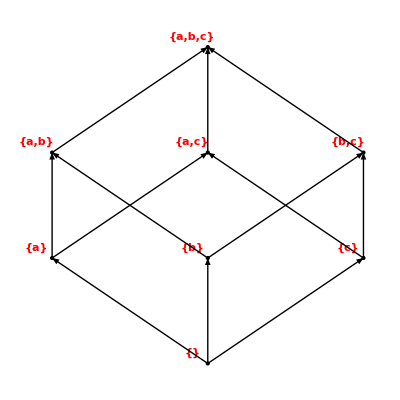

```mathematica
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=Partes;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

## Ejercicio 3 : Sea X = {a,b,c,d,e,f}, junto con la ordenación dada por el diagrama de orden indicado en el ejercicio, y sean Y={b,f,e} y Z={e,b,c,a} subconjuntos de X, se pide:

```mathematica
X={a,b,c,d,e,f};
Y={b,f,e};
Z={e,b,c,a};
R={
{a,a},{b,b},{c,c},{d,d},{e,e},{f,f},
{f,a},{f,b},{f,c},{f,d},{f,e},
{e,a},{e,b},{e,c},
{d,a},{d,b},
{b,a}
};
```

### a) Cotas superiores e inferiores de Y y de Z. ¿Existen supremo e ínfimo?

```mathematica
COTASSUPERIORES[X,Y,R]
SUPREMO[X,Y,R]
COTASINFERIORES[X,Y,R]
INFIMO[X,Y,R]
```

{a,b}

{b}

{f}

{f}

```mathematica
COTASSUPERIORES[X,Z,R]
SUPREMO[X,Z,R]
COTASINFERIORES[X,Z,R]
INFIMO[X,Z,R]
```

{}

{}

{e,f}

{e}

### b) Máximos y mínimos de Y y Z

```mathematica
MAXIMO[Y,R]
MINIMO[Y,R]
```

{b}

{f}

```mathematica
MAXIMO[Z,R]
MINIMO[Z,R]
```

{}

{e}

### c) Elementos maximales y minimales de X,Y y Z.

```mathematica
MAXIMALES[X,R]
MINIMALES[X,R]
```

{a,c}

{f}

```mathematica
MAXIMALES[Y,R]
MINIMALES[Y,R]
```

{b}

{f}

```mathematica
MAXIMALES[Z,R]
MINIMALES[Z,R]
```

{c,a}

{e}

### d) Representa el diagrama de orden de X, Y y Z.

Primero hay que rehacer las relaciones de orden para que no incluyan elementos que no estén en Y y Z. El diagrama de orden de X es:

Diagrama de orden:

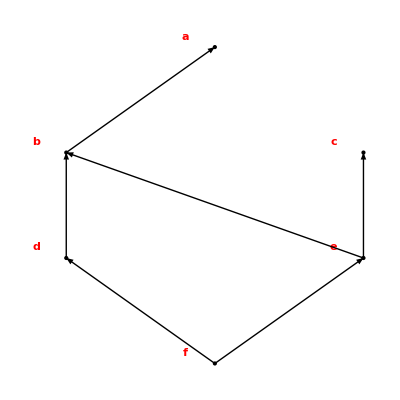

```mathematica
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
A = X;
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

Para Y, su relación de orden y diagrama:

```mathematica
R
```

{{b,a},{d,b},{e,b},{e,c},{f,d},{f,e}}

```mathematica
RY={{b,b},{e,e},{f,f},{f,b},{f,e},{e,b}}
```

{{b,b},{e,e},{f,f},{f,b},{f,e},{e,b}}

Diagrama de orden:

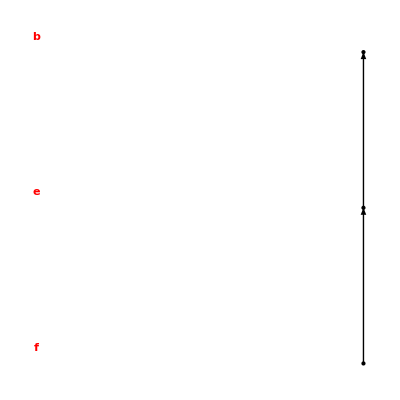

```mathematica
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
A = Y;
R = RY;
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

Y para Z, su relación de orden y diagrama de Hasse:

```mathematica
R
```

{{e,b},{f,e}}

```mathematica
RZ={{a,a},{b,b},{c,c},{e,e},{e,a},{e,b},{e,c},{b,a}}
```

{{a,a},{b,b},{c,c},{e,e},{e,a},{e,b},{e,c},{b,a}}

Diagrama de orden:

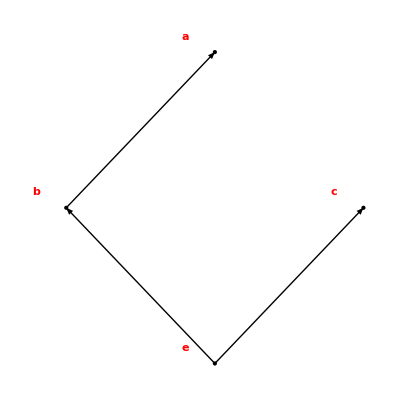

```mathematica
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
A = Z;
R = RZ;
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```